```mathematica
(*1*)
DSolve[y'[x]==Sin[5x],y[x],x]
```

{{y[x]→C[1]-1/5 Cos[5 x]}}

```mathematica
(*2a*)
DSolve[x^2*y'[x]==y[x]-y[x]*x,y[x],x]
```

{{y[x]→(ⅇ^(-1/x) C[1])/x}}

```mathematica
(*2b eikhane special solution akare chaile aivabe korte hobe mainly initial value akare thakle aivabe korte hoi*)
```

```mathematica
DSolve[{x^2*y'[x]==y[x]-y[x]*x,y[1]==1/E},y[x],x]
```

{{y[x]→ⅇ^(-1/x)/x}}

```mathematica
(*3a*)
DSolve[y''[x]+5*y'[x]+2*y[x]==0,y[x],x]
```

{{y[x]→ⅇ^((-5/2-(√17)/2) x) C[1]+ⅇ^((-5/2+(√17)/2) x) C[2]}}

```mathematica
(*Clear[x,y]*)
```

```mathematica
(*3b*)
DSolve[{y''[x]+5*y'[x]+2*y[x]==0,y[0]==5,y'[0]==10},y[x],x]
```

{{y[x]→-5/34 (-17 ⅇ^((-5/2-(√17)/2) x)+9 √17 ⅇ^((-5/2-(√17)/2) x)-17 ⅇ^((-5/2+(√17)/2) x)-9 √17 ⅇ^((-5/2+(√17)/2) x))}}

```mathematica
(*4*)
NSolve[16 x^2+13x+5==0,x]
```

{{x→-0.40625-0.384006 ⅈ},{x→-0.40625+0.384006 ⅈ}}

```mathematica
a=NDSolve[{y''[x]+x*y[x]==0,y[0]==1,y[1]==1},y[x],{x,0,10}]
```

{{y[x]→InterpolatingFunction[{{0.,10.}},<>][x]}}

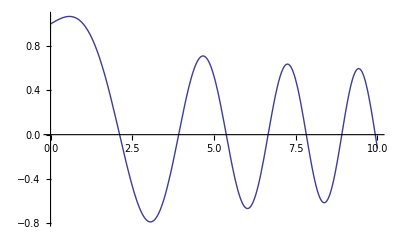

```mathematica
Plot[Evaluate[ReplaceAll[y[x],a]],{x,0,10}]
```

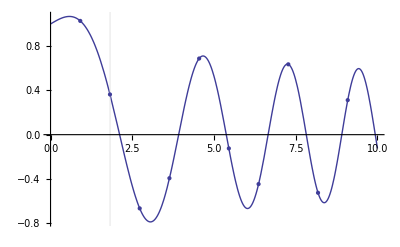

```mathematica
Plot[Evaluate[ReplaceAll[y[x],a]],{x,0,10},Mesh-> 10,GridLines-> {{1.82},None}]
```

```mathematica
Evaluate[a[1.82]]
```

{{y[x]→InterpolatingFunction[{{0.,10.}},<>][x]}}[1.82]

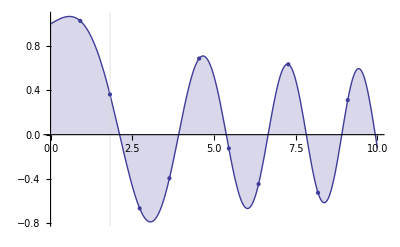

```mathematica
Plot[Evaluate[ReplaceAll[y[x],a]],{x,0,10},Mesh-> 10,GridLines-> {{1.82},None},Filling-> Axis]
```

```mathematica
v=NDSolve[{y''[t]+(y'[t]+1)^2*y'[t]+y[t]==0,y[0]==1,y'[0]==0},y[t],{t,0,10}]
```

{{y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

```mathematica
NDSolve[{y'[x]==x^2+√y[x],y[0]==1},y[x],{x,0,1}]
```

{{y[x]→InterpolatingFunction[{{0.,1.}},<>][x]}}

```mathematica
p=NDSolve[{y''[t]+(y'[t]+1)^2*y'[t]+y[t]==0,y[0]==1,y'[0]==0},y[t],{t,0,10}]
```

{{y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

```mathematica
equation=NDSolve[{y''[x]+y[x]==0,y[0]==0,y'[0]==1},y[x],{x,0,1000}]
```

{{y[x]→InterpolatingFunction[{{0.,1000.}},<>][x]}}

```mathematica
d=NDSolve[{y''[x]+y[x]==0,y[0]==0,y'[0]==1},y[x],{x,0,10}]
```

{{y[x]→InterpolatingFunction[{{0.,10.}},<>][x]}}

```mathematica
c=NDSolve[{y''[x]+0.3*y'[x]+Sin[y[x]]==0,y[0]==2,y'[0]==0},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0.,30.}},<>]}}

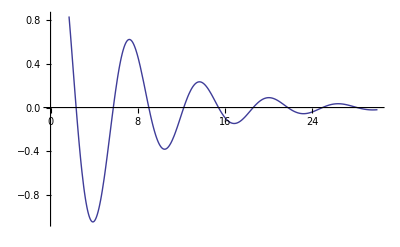

{{Q[t]→ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)) C[1]+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)) C[2]-(2 C L (√C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) R-√C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) R+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) √(-4 L+C R^2)+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) √(-4 L+C R^2)+2 √C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) j L ω-2 √C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) j L ω) V_0)/(√(-4 L+C R^2) (-√C R+√(-4 L+C R^2)-2 √C j L ω) (√C R+√(-4 L+C R^2)+2 √C j L ω))}}

```mathematica
Plot[Evaluate[y[x]/.c],{x,0,30}]
DSolve[Subscript[V, 0]*E^(j*ω*t)==Q[t]/C+L*Q''[t]+R*Q'[t],Q[t],t]
```

```mathematica
DSolve[Subscript[V, 0]*E^(j*ω*t)==(i[t])^2/(2C)+L*i'[t]+R*i[t],i[t],t]
```

{{i[t]→(2 C L (-1/(2 L)ⅈ^(R/(j L ω)) ⅇ^(-(R t)/(2 L)) R BesselI[R/(j L ω),(√2 √(ⅇ^(j t ω) V_0))/(√C j L ω)] Gamma[1+R/(j L ω)]+(ⅈ^(R/(j L ω)) ⅇ^(-(R t)/(2 L)+j t ω) (BesselI[-1+R/(j L ω),(√2 √(ⅇ^(j t ω) V_0))/(√C j L ω)]+BesselI[1+R/(j L ω),(√2 √(ⅇ^(j t ω) V_0))/(√C j L ω)]) Gamma[1+R/(j L ω)] V_0)/(2 √2 √C L √(ⅇ^(j t ω) V_0))+C[1] (-1/(2 L)ⅈ^(-R/(j L ω)) ⅇ^(-(R t)/(2 L)) R BesselI[-R/(j L ω),(√2 √(ⅇ^(j t ω) V_0))/(√C j L ω)] Gamma[1-R/(j L ω)]+(ⅈ^(-R/(j L ω)) ⅇ^(-(R t)/(2 L)+j t ω) (BesselI[-1-R/(j L ω),(√2 √(ⅇ^(j t ω) V_0))/(√C j L ω)]+BesselI[1-R/(j L ω),(√2 √(ⅇ^(j t ω) V_0))/(√C j L ω)]) Gamma[1-R/(j L ω)] V_0)/(2 √2 √C L √(ⅇ^(j t ω) V_0)))))/(ⅈ^(-R/(j L ω)) ⅇ^(-(R t)/(2 L)) BesselI[-R/(j L ω),(√2 √(ⅇ^(j t ω) V_0))/(√C j L ω)] C[1] Gamma[1-R/(j L ω)]+ⅈ^(R/(j L ω)) ⅇ^(-(R t)/(2 L)) BesselI[R/(j L ω),(√2 √(ⅇ^(j t ω) V_0))/(√C j L ω)] Gamma[1+R/(j L ω)])}}

```mathematica
Plot[Evaluate[y[x]/.c],{x,0,30}]
```

-Graphics-

```mathematica
DSolve[y'[x]==y[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]}}

```mathematica
DSolve[y''[x]==y[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x C[2]}}

```mathematica
DSolve[y'''[x]==y[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(-x/2) C[2] Cos[(√3 x)/2]+ⅇ^(-x/2) C[3] Sin[(√3 x)/2]}}

```mathematica
DSolve[y''''[x]==y[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x C[3]+C[2] Cos[x]+C[4] Sin[x]}}

```mathematica
DSolve[y'''''[x]==y[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^((-1/4-(√5)/4) x) C[3] Cos[√(5/8-(√5)/8) x]+ⅇ^((-1/4+(√5)/4) x) C[2] Cos[√(5/8+(√5)/8) x]+ⅇ^((-1/4-(√5)/4) x) C[4] Sin[√(5/8-(√5)/8) x]+ⅇ^((-1/4+(√5)/4) x) C[5] Sin[√(5/8+(√5)/8) x]}}

```mathematica
sol=DSolve[{y'[x]==y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^x}}

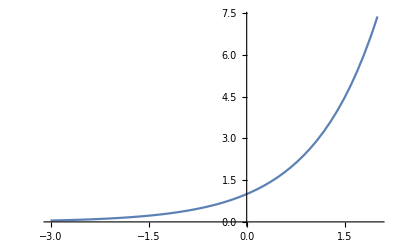

```mathematica
Plot[y[x]/.sol,{x,-3,2}]
```